Author:  Archisman Panigrahi
Research Article: Non-Fermi liquids from subsystem symmetry breaking in van der Waals multilayers, A. Panigrahi and A. Kumar (2024).

This Mathematica notebook plots the data obtained with the Julia program identical_parabolic_many_bands_constant_density_realistic_parameters.ipynb

First part: Δ vs density plot at fixed temperature

```mathematica
(** Nz = 10, eps_r = 12.5, m*_parallel = 0.07 m_e, dz = 3 angstrom, k_B T = 0.05 meV**)
```

```mathematica
densityArray = 5*Table[n,{n,1,20}] (**In units of 10^10/cm^2 **)
```

{5,10,15,20,25,30,35,40,45,50,55,60,65,70,75,80,85,90,95,100}

```mathematica
DeltaArray={1.265,1.697,2.057,2.324,2.519,2.538,2.606,2.695,2.765,2.854,2.901,3.029,2.700,2.184,1.815,1.322,1.056,1.044,0.897,0.895}
```

{1.265,1.697,2.057,2.324,2.519,2.538,2.606,2.695,2.765,2.854,2.901,3.029,2.7,2.184,1.815,1.322,1.056,1.044,0.897,0.895}

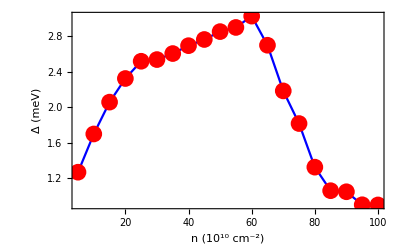

```mathematica
Show[ListPlot[Transpose[{densityArray,DeltaArray}],Joined->True,PlotMarkers->{Automatic,10},PlotStyle->{Blue},Epilog->{PointSize[0.03],Red,Point[Transpose[{densityArray,DeltaArray}]]}],Frame->True,FrameStyle->Directive[Thick,Black],FrameLabel->{Style["n (10^10 cm^-2)" ,22],Style["Δ (meV)",22]},FrameTicksStyle->Directive[Black,22],LabelStyle->Directive[Black,14],GridLines->None,PlotRange->All]
```

Second part : Δ vs Temperature plot at fixed density

```mathematica
(** Nz = 10, eps_r = 12.5, m*_parallel = 0.07 m_e, dz = 3 angstrom, n=55*10^10/cm^2 **)
```

```mathematica
(* 1 meV = 11.6045 Kelvin * k_B *)
```

```mathematica
kbTArray={0.05,0.15,0.3,0.45,0.6,0.75,0.9,1.05,1.2,1.35,1.5,1.65,1.75,1.8}*11.6045
```

{0.580225,1.74068,3.48135,5.22203,6.9627,8.70338,10.4441,12.1847,13.9254,15.6661,17.4068,19.1474,20.3079,20.8881}

```mathematica
DeltavsTArray={2.92,2.948,2.911,2.833,2.72,2.603,2.458,2.28,2.077,1.819,1.483,0.988,0.3299,0.026}
```

{2.92,2.948,2.911,2.833,2.72,2.603,2.458,2.28,2.077,1.819,1.483,0.988,0.3299,0.026}

```mathematica
Dimensions[kbTArray]
```

{14}

```mathematica
Dimensions[DeltavsTArray]
```

{14}

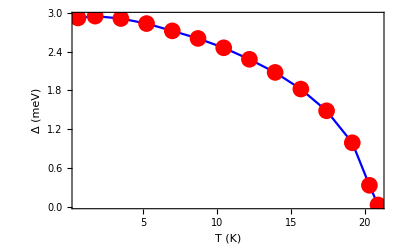

```mathematica
Show[ListPlot[Transpose[{kbTArray,DeltavsTArray}],Joined->True,PlotMarkers->{Automatic,10},PlotStyle->{Blue},Epilog->{PointSize[0.03],Red,Point[Transpose[{kbTArray,DeltavsTArray}]]}],Frame->True,FrameStyle->Directive[Thick,Black],FrameLabel->{Style["T (K)" ,22],Style["Δ (meV)",22]},FrameTicksStyle->Directive[Black,22],LabelStyle->Directive[Black,18],GridLines->None,PlotRange->All]
```